```mathematica
Clear["Global`*"]
```

```mathematica
a=2.46;(*a is given in units of 10^-10*)
γ0=3.1;
γ1=0.38;
γ2=-0.015;
γ3=0.29;
γ4=0.141;
δ=-0.0105;
Δ1=0.05;
Δ2=-0.0023;
(*γ1=0.;
γ2=0.;
γ3=0.;
γ4=0.;
δ=0.;
Δ1=0.;
Δ2=0.;*)
u[kx_,ky_]=1.+2.*Cos[0.5*kx*a]*Exp[-ⅈ*ky*a*0.5*√3];
v[kx_,ky_]=Exp[ⅈ*ky*a*√3]*u[kx,ky];
Hk[kx_,ky_]={{Δ1+Δ2,-γ0*u[kx,ky],γ4*u[kx,ky]*,γ1,0,0},{-γ0*u[kx,ky]*,Δ1+Δ2+δ,γ3*v[kx,ky],γ4*u[kx,ky]*,0.5*γ2,0},{γ4*u[kx,ky],γ3*v[kx,ky]*,-2.*Δ2,-γ0*u[kx,ky],γ4*v[kx,ky]*,γ1},{γ1,γ4*u[kx,ky],-γ0*u[kx,ky]*,-2.*Δ2,γ3*u[kx,ky],γ4*u[kx,ky]*},{0,0.5*γ2,γ4*v[kx,ky],γ3*u[kx,ky]*,Δ2-Δ1+δ,-γ0*v[kx,ky]},{0,0,γ1,γ4*u[kx,ky],-γ0*v[kx,ky]*,Δ2-Δ1}};
(*Number of bands*)
Nb=Length[Hk[kx,ky]];
```

```mathematica
μ=-0.057;(*0.065*γ0;Chemical potential. VHS is at μ=-0.052175;*)
kbT=0.0000861*1; (*Boltzmann's k × temperature*)
η=0.000001;(*Self energy*) 
δc=10.*kbT;
FDif[ϵk_]=If[Abs[μ-ϵk]<δc,1/(1+Exp[(ϵk-μ)/kbT]),UnitStep[μ-ϵk]];
δFif[ϵk_]=If[Abs[μ-ϵk]<δc,-1./kbT/(2*(1+Cosh[(ϵk-μ)/kbT])),0.];
```

```mathematica
Nk=150;(*k-mesh will have Nk^2 points, Nk>1, integer*)
StringForm["The k-mesh has `` points.",Nk^2]
Λk=1; (*A factor controlling the size of the mesh in k space*)
Δk=Λk/Nk; (*Spacing between k-points*)

b=(4π)/(√3*a); (*Magnitude of reciprocal vectors*)
b1=b*{(-√3)/2,1/2}; (*Reciprocal vectors b1,b2*)
b2=b*{(√3)/2,1/2};
lineb1=Arrow[{{0,0},b1}]; 
lineb2=Arrow[{{0,0},b2}]; 
BZcontour = Polygon[{((4π)/(3a))*{-1,0},((4π)/(3a))*{(-1)/2,(√3)/2},((4π)/(3a))*{1/2,(√3)/2},((4π)/(3a))*{1,0},((4π)/(3a))*{1/2,(-√3)/2},((4π)/(3a))*{(-1)/2,(-√3)/2}}];
kaMesh=Flatten[Table[{(j-i)*Δk*b*((√3)/2),(j+i)*Δk*b*(1/2)},{i,1,Nk,1},{j,1,Nk,1}],1]; (*k-mesh first generated by reciprocal vectors *)
kaMesh1BZ=kaMesh-TensorProduct[(1-UnitStep[kaMesh.b2])*UnitStep[kaMesh.(b1+b2)]*Floor[kaMesh.b1/b^2+0.5],b1]-TensorProduct[(1-UnitStep[kaMesh.b1])*UnitStep[kaMesh.(b1+b2)]*Floor[kaMesh.b2/b^2+0.5],b2]-TensorProduct[UnitStep[kaMesh.b1]*UnitStep[kaMesh.b2]*Floor[kaMesh.(b1+b2)/b^2+0.5],(b1+b2)]; (*Moving all k-points to 1BZ*)
(*Increasing covered area of the 1BZ*)
kaMesh1BZ=kaMesh1BZ*0.03;
(*MOVING K MESH TO K POINT*)
kaMesh1BZ=(kaMesh1BZᵀ+1.0*{(4π)/(3a),0})ᵀ;
kaMeshKpoint= kaMesh1BZ;
kaMesh1BZ=kaMesh1BZ-1*TensorProduct[UnitStep[kaMesh1BZ[[All,1]]*kaMesh1BZ[[All,2]]]*Floor[kaMesh1BZ.b2/b^2+0.5],b2]-1*TensorProduct[(1-UnitStep[kaMesh1BZ[[All,1]]*kaMesh1BZ[[All,2]]])*Floor[kaMesh1BZ.b1/b^2+0.5],b1];

qaMesh1BZKpΓK=DeleteCases[kaMesh1BZ,{kx_,ky_}/; ky≠0]; (*Defining q-path as all points with ky=0. This is K'->Γ->K *)
```

The k-mesh has 22500 points.

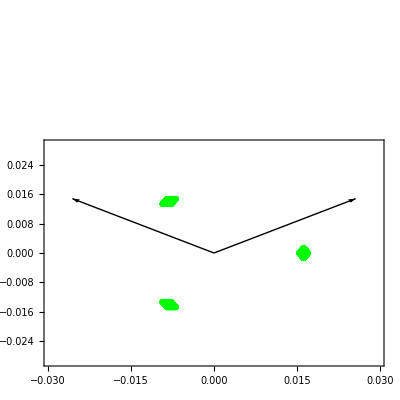

```mathematica
Show[ListPlot[{kaMesh1BZ},AspectRatio->Automatic,Epilog->{lineb1,lineb2,Text["b_1",b1+{0,0.2}],Text["b_2",b2+{0,0.2}]},AspectRatio->Automatic,PlotMarkers->{Graphics[{Green,Disk[{0,0}]}],0.01},PlotStyle->Blue,PlotRange->{{-b,b},{-b,b}},Frame->True], Graphics[{Red,Opacity[0.],EdgeForm [Dashed],BZcontour}] ]
```

-0.057

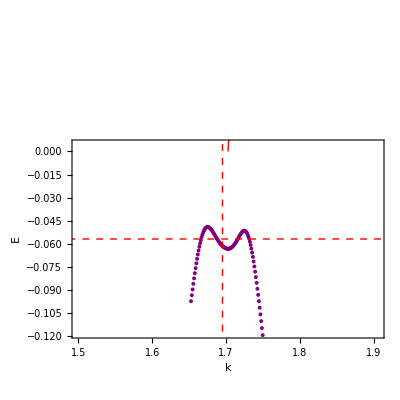

-0.055

```mathematica
Eψk=Map[Eigensystem,Apply[Hk,kaMeshKpoint,{1}]];
Enkp=Eψk[[All,1]];
(*EsurfKp=Flatten[Table[Flatten[{kaMesh1BZ[[i]],Enkp[[i,j]]}],{i,Nk^2},{j,Nb}],1];
ListPointPlot3D[EsurfKp,AspectRatio->1]
ListPlot[{kaMesh1BZ},AspectRatio->Automatic,AspectRatio->Automatic,PlotMarkers->{Graphics[{Green,Disk[{0,0}]}],0.01},PlotStyle->Blue,PlotRange->{{-ba,ba},{-ba,ba}},Frame->True]
*)
iqp=Flatten[Position[kaMeshKpoint ,{kx_,ky_} /; ky==0]];
EpathKp=Flatten[Table[Flatten[{kaMeshKpoint [[iqp[[i]]]][[1]],Enkp[[iqp[[i]],j]]}],{i,Length[iqp]},{j,Nb}],1];
EF=Line[{{-(4π)/(3a),μ},{2*(4π)/(3a),μ}}]; (*Fermi level*)
qF=Line[{{(4π)/(3.*a)+μ/(1*γ0*a),-4*γ0},{(4π)/(3.*a)+μ/(1*γ0*a),4*γ0}}];
Dirac=Line[{{(4π)/(3.*a)+0,0},{(4π)/(3.*a)+1,γ0*a*1}}];
(*To visualize μ better:
δK  = 0.3/a;
δE = 0.02*γ0;
*)
(*Fuller view *)
δK  = 0.5/a;
δE = 0.02*γ0;
k0= (4π)/(3a);
E0=μ

Show[ListPlot[EpathKp,PlotRange->{{k0-δK,k0+δK},{E0-δE,E0+δE}},Joined->False,AspectRatio->1,PlotMarkers->{Automatic, Tiny},PlotStyle->Purple,Frame->True,FrameLabel->{"k","E"}],Graphics[{Red,Dashed,EF}],Graphics[{Red,Dashed,qF}],Graphics[{Red,Thick,Dirac}],Graphics[{Red,Text[{Style["μ=",Medium],μ},{(4π)/(3a),μ+1}]}],Graphics[{Red,Text[{Style["q_F=",Medium],μ/(γ0*a)},{μ/(γ0*a)+1,4*γ0+0.5}]}]]
```

```mathematica
(*Defining parameters for sampling in q*)
Nq=60
Lq=0.06;(*(4π)/(3a)*0.05;*)
Δq=Lq/Nq;

qi=Table[{0.*(-Lq/2)+i*Δq,0.},{i,0,Nq}];
ω=0.;
```

60

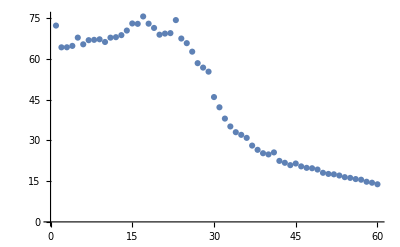

```mathematica
(*Calculating polarizability for q-path*)
Eψk=Map[Eigensystem,Apply[Hk,kaMesh1BZ,{1}]];
Enk=Eψk[[All,1]];
ψnk=Eψk[[All,2]];
ψnk=Map[Normalize,ψnk,{2}];
(*kqaMesh1BZ=kaMesh1BZ; (*Starting with q={0.,0.}*)*)
kqaMesh1BZ=(kaMesh1BZᵀ-0.0*{(4π)/(3a),0})ᵀ;(*Starting to the left of Γ*)
kqaMesh1BZ=kqaMesh1BZ-1*TensorProduct[UnitStep[kqaMesh1BZ[[All,1]]*kqaMesh1BZ[[All,2]]]*Floor[kqaMesh1BZ.b2/b^2+0.5],b2]-1*TensorProduct[(1-UnitStep[kqaMesh1BZ[[All,1]]*kqaMesh1BZ[[All,2]]])*Floor[kqaMesh1BZ.b1/b^2+0.5],b1];

Πq0=Table[0,{i,0,Nq}];
(*The q=0 point:*)
(*
Πq0[[1]] = -(2/Nk^2)*Total[Map[-1/(2*kbT*(1+Cosh[(#-μ)/kbT]))&,Enk],2];
*)
q=0.; (*Used for progress bar only*)
Monitor[
For[i=0,i≤Nq,i++,
q=i*Δq; (*Not being used*)

Eψkq=Map[Eigensystem,Apply[Hk,kqaMesh1BZ,{1}]];
Enkq= Eψkq[[All,1]];
ψnkq=Eψkq[[All,2]];
ψnkq=Map[Normalize,ψnkq,{2}];
(*
nfEk=Map[1/(1+Exp[(#-μ)/kbT])&,Enk];
nfEkq=Map[1/(1+Exp[(#-μ)/kbT])&,Enkq];

nfEk=Map[FDif[#]&,Enk,{2}];
nfEkq=Map[FDif[#]&,Enkq,{2}];
*)
nfEk=Map[UnitStep[μ-#]&,Enk,{2}];
nfEkq=Map[UnitStep[μ-#]&,Enkq,{2}];
(*if ΔE[i]=0., then make ΔE[i]=1., Δnf[i]=δf[i]. To determine which ΔE[i]=0, get indices of elements under threshold, then use those indicies to change Δnf,δf.
Position[Abs[Flatten[ΔE]],_?(# < η &)]*)
Δnf=Flatten[Table[Tuples[{nfEk[[i]],nfEkq[[i]]}][[All,1]]-Tuples[{nfEk[[i]],nfEkq[[i]]}][[All,2]],{i,Nk^2}]];
ΔE=Flatten[Table[Tuples[{Enk[[i]],Enkq[[i]]}][[All,1]]-Tuples[{Enk[[i]],Enkq[[i]]}][[All,2]],{i,Nk^2}]]+ω;(*+ⅈ*η*)
(*δf=Flatten[Map[-1/(2*kbT*(1+Cosh[(#-μ)/kbT]))&,Table[Tuples[{Enk[[i]],Enkq[[i]]}][[All,1]],{i,Nk^2}]]];*)
ψTuples=Table[Tuples[{ψnk[[i]],ψnkq[[i]]*}],{i,Nk^2}];
Fkq=Flatten[Table[Abs[ψTuples[[i]][[j]][[1]].ψTuples[[i]][[j]][[2]]]^2,{i,Nk^2},{j,Nb^2}]];
idiv=Flatten[Position[Abs[ΔE],_?(#==0.&)]];
ΔE[[idiv]]=1.;
(*Fkq[[idiv]]=1.;*)

(*
Δnf[[idiv]]=Map[-1/(2*kbT*(1+Cosh[(#-μ)/kbT]))&,Flatten[Table[Tuples[{Enk[[i]],Enkq[[i]]}][[All,1]],{i,Nk^2}]][[idiv]]];
*)
Δnf[[idiv]]=Map[δFif[#]&,Flatten[Table[Tuples[{Enk[[i]],Enkq[[i]]}][[All,1]],{i,Nk^2}]][[idiv]]];

Πq0[[i+1]]=-(2/Nk^2)*Total[Δnf*Re[1/ΔE]*Fkq];(**((ω)/Norm[q]^2)... -0.*η*Im[1/ΔE]*δf *)
kqaMesh = (kqaMesh1BZᵀ+{Δq,0})ᵀ;

kqaMesh1BZ = kqaMesh-1*TensorProduct[UnitStep[kqaMesh.(b1+b2)]*Floor[kqaMesh.b2/b^2+0.5],b2]-1*TensorProduct[(1-UnitStep[kqaMesh.(b1+b2)])*Floor[kqaMesh.b1/b^2+0.5],b1]
]
,Grid[{{Text[Style["Progress:",Darker[Blue,0.66]]],ProgressIndicator[q,{0.,Lq*1.05}],StringForm["``%",NumberForm[100*q/(Lq*1.05),{3,2}]]},{Text[Style["Current value of q: ",Darker[Blue,0.66]]],q ,StringForm["Final value: ``",NumberForm[Lq]] }},Alignment->Left,Dividers->Center]];
ListPlot[Table[{i,Re[Πq0[[i]]]},{i,1,Nq}]]
```

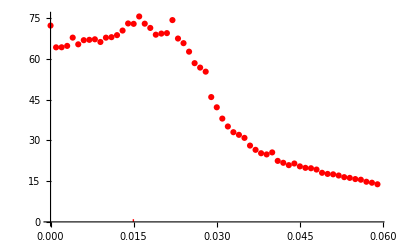

```mathematica
Show[ListPlot[Table[{qi[[i,1]],Re[Πq0[[i]]]},{i,1,Nq}],PlotRange->All,PlotStyle-> Red],Graphics[{Red,Line[{{-2*μ/(γ0*a),0},{-2*1μ/(γ0*a),1}}]}]]
```

```mathematica
EmitSound[Play[Sin[10*π*t]SawtoothWave[880*2 Pi t],{t,0,0.5}]]
```

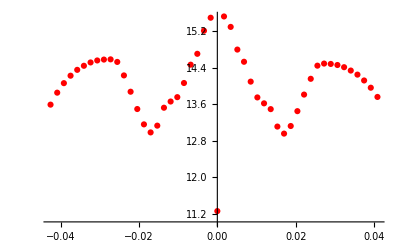

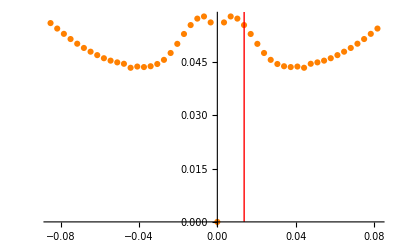
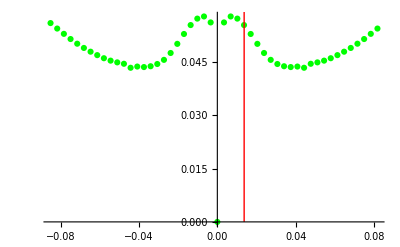
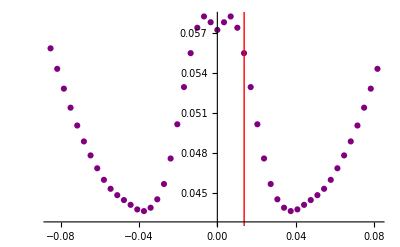
```mathematica
Show[-Graphics-,-Graphics-,-Graphics-](*Before and after flattening before summing over k. Purple: after removing self energy from denominator. We are now subsituting δf for Abs[ΔE]<η, η=0.001,Nk=50*)
```

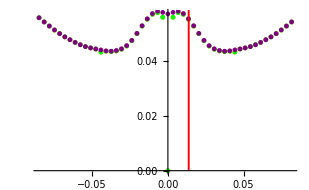

```mathematica
A={1,2,-4,6,8+ⅈ,10};
B=Abs[Re[A]]
B[[{2,5}]]={kk,qq};
B

(*Position[B,_?(#<η&)]*)
```

{1,2,4,6,8,10}

{1,kk,4,6,qq,10}

```mathematica
Enkt={{e1k1,e2k1,e3k1},{e1k2,e2k2,e3k2}};
Enkqt={{e1q1,e2q1,e3q1},{e1q2,e2q2,e3q2}};
i=2;
Tuples[{Enkt[[i]],Enkqt[[i]]}][[All,1]][[{1,4,7}]]
Tuples[{Enkt[[i]],Enkqt[[i]]}][[All,1]]-Tuples[{Enkt[[i]],Enkqt[[i]]}][[All,2]]
```

{e1k2,e2k2,e3k2}

{e1k2-e1q2,e1k2-e2q2,e1k2-e3q2,-e1q2+e2k2,e2k2-e2q2,e2k2-e3q2,-e1q2+e3k2,-e2q2+e3k2,e3k2-e3q2}

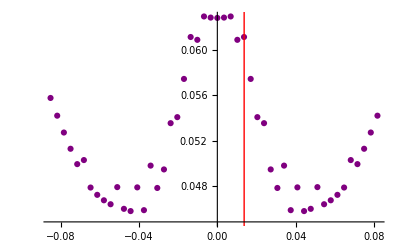
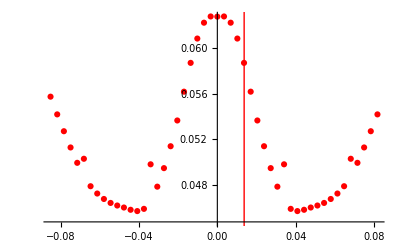
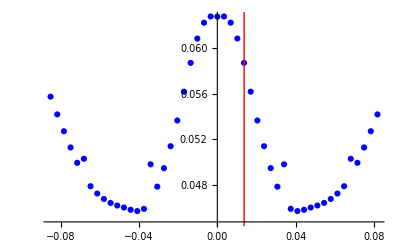
```mathematica
Show[-Graphics-,-Graphics-,-Graphics-](*Purple: Same but for Nk=150. Red: Same but η=0.0001, this fixed the points closer to q=0*)
```

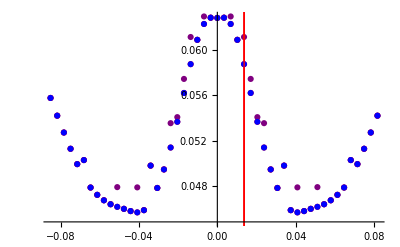

```mathematica
(*Started at pm 5/3/21*)(*calcualting same resolution but for the main cuadrant ω,q<1.25*)(**)
Monitor[Table[Pause[0.001],{ω,0.625,1.25,(1.25-0.625)/20},{q,0.01,0.625,(0.625-0.01)/20}],Grid[{{Text[Style["Progress:",Darker[Blue,0.66]]],ProgressIndicator[ω,{0.625,1.25}],StringForm["``%",NumberForm[100*(ω-0.625)/(1.25-0.625),{3,2}]]},{Text[Style["Current value of ω: ",Darker[Blue,0.66]]],ω ,StringForm["Final value: ``",NumberForm[1.25]] }},Alignment->Left,Dividers->Center]];
```

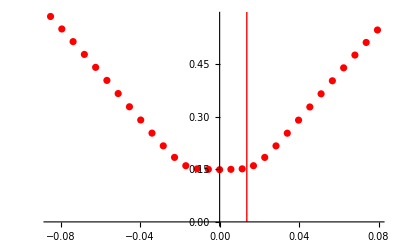
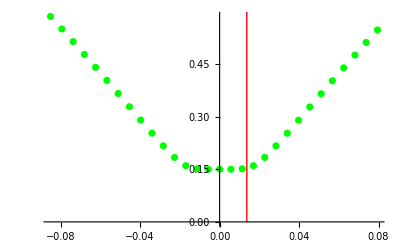
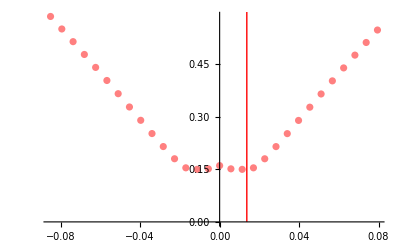
```mathematica
Show[-Graphics-,-Graphics-,-Graphics-] (*Nk=150, kamesh*0.2, K-centered, graphene parameters. Div condition # < 0. fixed problems at q=0,q_\pm. Removed Fkq=1. it didn.b4t appear to make difference.Green: Nk=200, almost no diff., a little diff at q=0. Pink: kbT=0.05 mK (the other ones are at 0.1mK), looks flatter but seems to diverge at q=0 *)
```

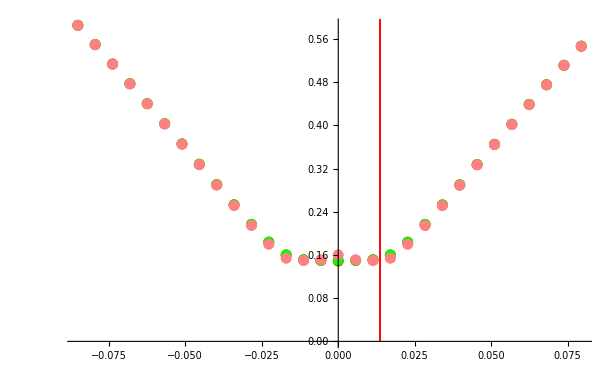

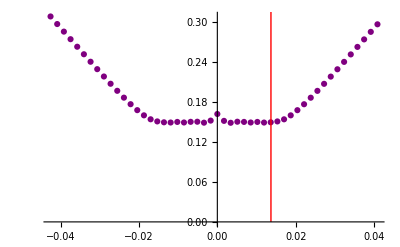
```mathematica
Show[-Graphics-](*Same but Nq=50, Lq=(4π)/(3a)*0.05*)
```

-Graphics-

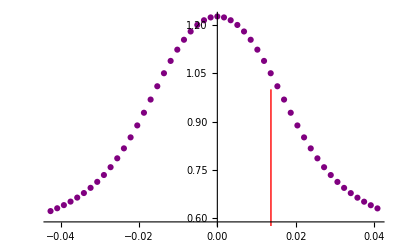
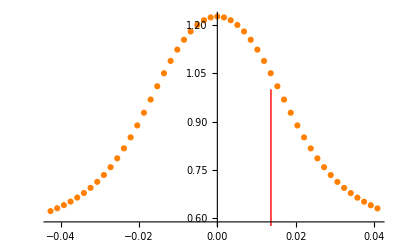
```mathematica
Show[-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-](*Same but for trilayer parameters, for Nk=200. Green: Nk=300 (didn't change). Yellow: kamesh*0.05. Nk=200 (didn't change), Orange: kamesh*0.2 (didnt change)*)
```

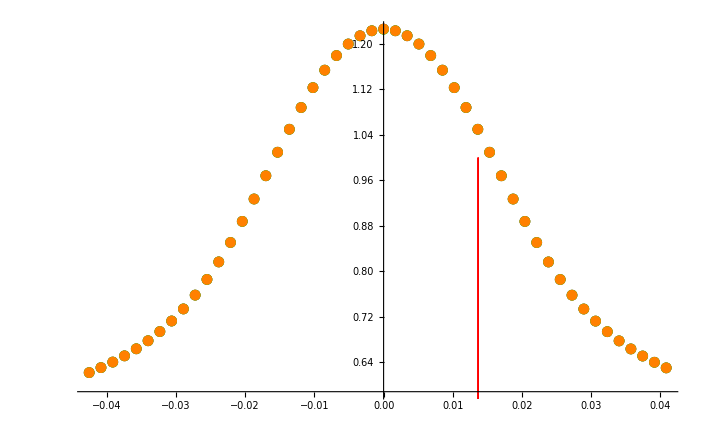

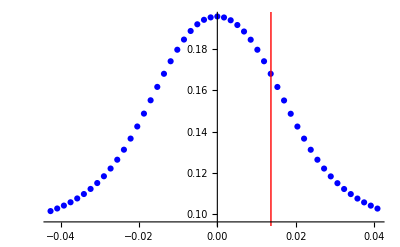
```mathematica
Show[-Graphics-](*Blue: kamesh*0.5, THE AMPLITUDE CHANGES A LOT*)
```

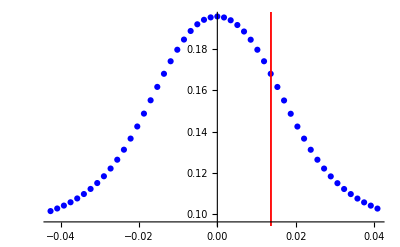

-Graphics-

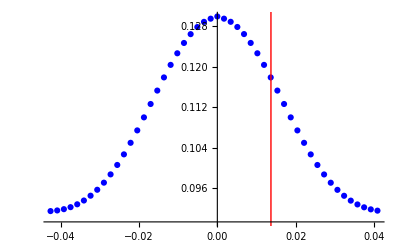
```mathematica
Show[-Graphics-] (*Green: T= 0.1mK (past plots were  at 0.05mk)*)
```

-Graphics-

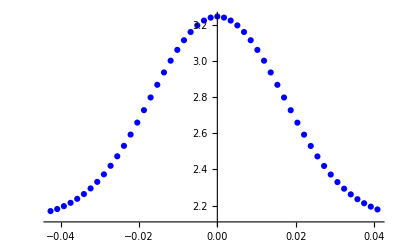
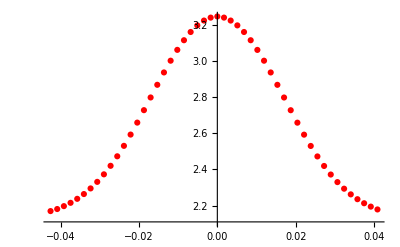
```mathematica
Show[-Graphics-,-Graphics-](*TESTING CUT FOR FD[ϵk].For Nk=50. Blue: before, Red: after. Seems to not have changed*)
```

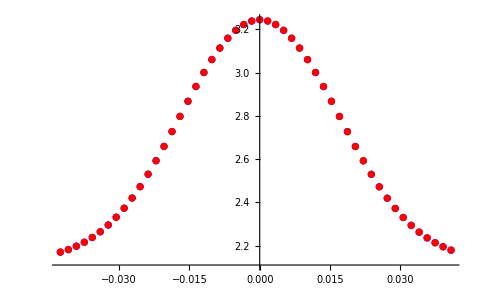

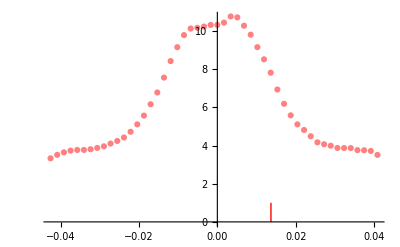
```mathematica
Show[-Graphics-] (*For T=0.01mk*)
```

-Graphics-

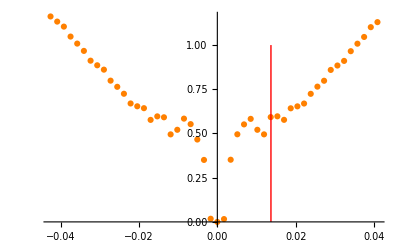
```mathematica
Show[-Graphics-] (*Graphene parameters. Nk=50, kamesh*0.05, K-centered, cut fermi distributions. T=0.01mK (now there are no errors of exponentials)*)
```

-Graphics-

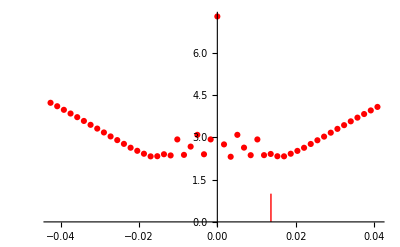
```mathematica
Show[-Graphics-](*Same but kamesh*0.05 (it got better!)*)
```

-Graphics-

```mathematica
Show[-Graphics-] (*Same but kamesh*0.02 (it got worse!)*)
```

-Graphics-

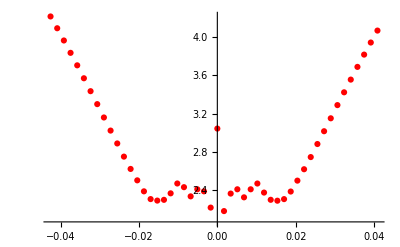
```mathematica
Show[-Graphics-](*Same but Nk=100*)
```

-Graphics-

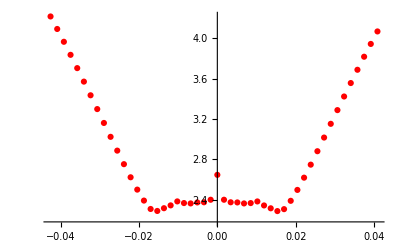
```mathematica
Show[-Graphics-] (*Nk=150*)
```

-Graphics-

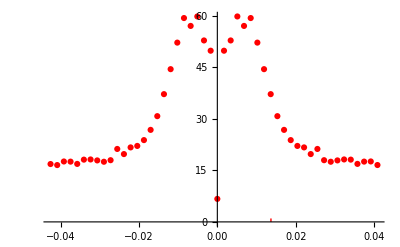
```mathematica
Show[-Graphics-](*Trilayer parameters, Nk=150, replacing FD by  UnitStep*)
```

-Graphics-

```mathematica
Show[-Graphics-](*Nk=150*)
```

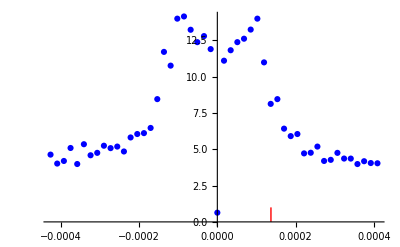
```mathematica
Show[-Graphics-](*a->s*a, s=100, T=5K*)
```

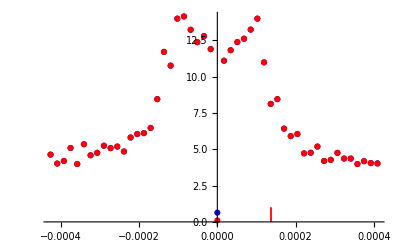

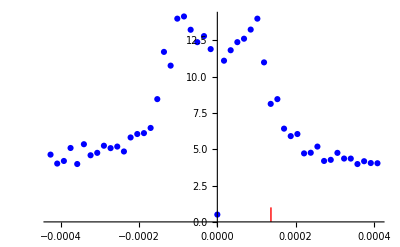
```mathematica
Show[-Graphics-](*T=10K*)
```

-Graphics-

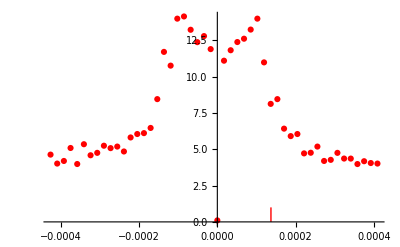
```mathematica
Show[-Graphics-] (*T=100K. Its not changing*)
```

-Graphics-

```mathematica
N[12*10^4]
```

120000.

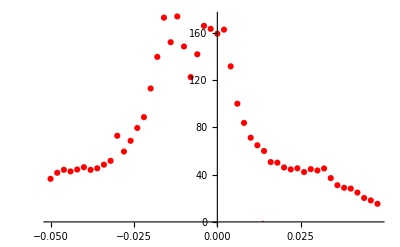
```mathematica
Show[-Graphics-] (*Trying to reproduce the results of Simplified model with realistic parameters. Nk=100, T=100K, kamesh*0.03, Lq=0.1, Nq= 50, μ=-0.052175, δc=10.*kbT. (my mistake, I didn't center on q, but maybe this is acually more accurate than I thought)*)
```

-Graphics-

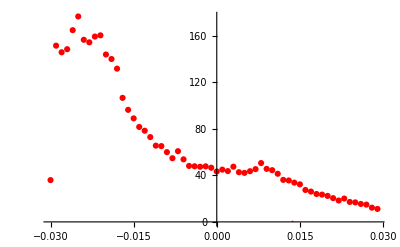
```mathematica
Show[-Graphics-] (*Nq=60, Starting at K point (instead of going through it from K-Lq/2 to K+Lq/2). Also Lq=0.06*)
```

-Graphics-

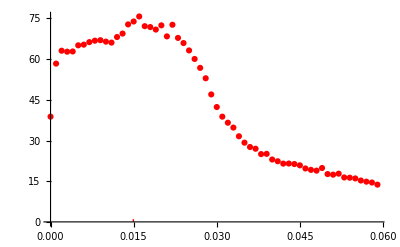
```mathematica
Show[-Graphics-] (*Same but μ=-0.57, also fixed the starting point of q path at K*)
```

-Graphics-

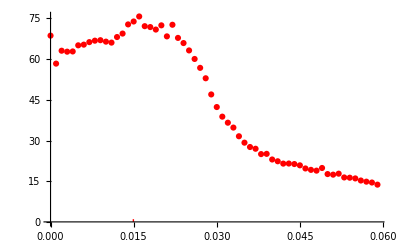
```mathematica
Show[-Graphics-] (*Same but T=10K*)
```

-Graphics-

```mathematica
Show[-Graphics-] (*Same but T=1K, Nk=150. You kind of see the 3 expected peaks, 2 around 0.02 and 1 around 0.4. The ones at low q is probably noise due to low Nk,as we've seen from the simplified model*)
```

-Graphics-